```mathematica
FourierTransform[Exp[-beta*Abs[t]]*Cos[nu*Abs[t]],t,ω]
```

(beta √(2/π) (beta^2+nu^2+ω^2))/(beta^4+2 beta^2 nu^2+nu^4+2 beta^2 ω^2-2 nu^2 ω^2+ω^4)

```mathematica
Simplify[%]
```

(beta √(2/π) (beta^2+nu^2+ω^2))/(beta^4+(nu^2-ω^2)^2+2 beta^2 (nu^2+ω^2))

```mathematica
Factor[%]
```

(beta √(2/π) (beta^2+nu^2+ω^2))/((beta^2+nu^2-2 nu ω+ω^2) (beta^2+nu^2+2 nu ω+ω^2))

```mathematica
Apart[%]
```

(beta √(2/π) (beta^2+nu^2+ω^2))/((beta^2+nu^2-2 nu ω+ω^2) (beta^2+nu^2+2 nu ω+ω^2))

```mathematica
Apart[Out[1]]
```

(beta √(2/π) (beta^2+nu^2+ω^2))/((beta^2+nu^2-2 nu ω+ω^2) (beta^2+nu^2+2 nu ω+ω^2))

```mathematica
Apart[%,ω]
```

beta/(√(2 π) (beta^2+nu^2-2 nu ω+ω^2))+beta/(√(2 π) (beta^2+nu^2+2 nu ω+ω^2))

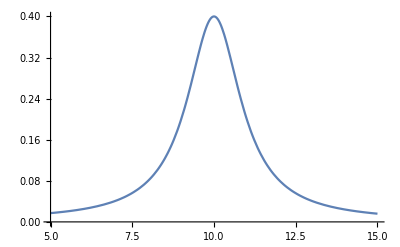

```mathematica
Plot[Out[6]/. beta -> 1 /. nu -> 10,{ω,5,15}]
```

```mathematica
Out[6]
```

beta/(√(2 π) (beta^2+nu^2-2 nu ω+ω^2))+beta/(√(2 π) (beta^2+nu^2+2 nu ω+ω^2))

```mathematica
InputForm[%]
```

beta/(Sqrt[2*Pi]*(beta^2 + nu^2 - 2*nu*ω + ω^2)) + 
 beta/(Sqrt[2*Pi]*(beta^2 + nu^2 + 2*nu*ω + ω^2))

```mathematica
Series[beta/Sqrt[2*Pi]/(beta^2+1/x^2-2*ω/x+ω^2) + beta/Sqrt[2*Pi]/(beta^2+1/x^2+2*ω/x+ω^2),{x,0,4}]
```

beta √(2/π) x^2+(-beta^3 √(2/π)+3 beta √(2/π) ω^2) x^4+O[x]^5

```mathematica
FourierTransform[Exp[-beta*Abs[t]]*Sin[nu*Abs[t]],t,ω]
```

(nu √(2/π) (beta^2+nu^2-ω^2))/(beta^4+2 beta^2 nu^2+nu^4+2 beta^2 ω^2-2 nu^2 ω^2+ω^4)

```mathematica
Apart[%,ω]
```

(nu √(2/π)-√(2/π) ω)/(2 (beta^2+nu^2-2 nu ω+ω^2))+(nu √(2/π)+√(2/π) ω)/(2 (beta^2+nu^2+2 nu ω+ω^2))

```mathematica
Simplify[Out[2]]
```

(nu √(2/π) (beta^2+nu^2-ω^2))/((beta^2+(nu-ω)^2) (beta^2+(nu+ω)^2))

```mathematica
Apart[%,ω]
```

(nu √(2/π)-√(2/π) ω)/(2 (beta^2+nu^2-2 nu ω+ω^2))+(nu √(2/π)+√(2/π) ω)/(2 (beta^2+nu^2+2 nu ω+ω^2))

```mathematica
Limit[%,ω -> Infinity]
```

0

```mathematica
InputForm[Out[5]]
```

(nu*Sqrt[2/Pi] - Sqrt[2/Pi]*ω)/(2*(beta^2 + nu^2 - 2*nu*ω + ω^2)) + 
 (nu*Sqrt[2/Pi] + Sqrt[2/Pi]*ω)/(2*(beta^2 + nu^2 + 2*nu*ω + ω^2))

```mathematica
Series[(nu-1/x)/(b2+(nu-1/x)^2) + (nu+1/x)/(b2+(nu+1/x)^2),{x,0,3}]
```

-2 nu x^2+O[x]^4

```mathematica
Simplify[Out[1]]
```

(nu √(2/π) (beta^2+nu^2-ω^2))/(beta^4+(nu^2-ω^2)^2+2 beta^2 (nu^2+ω^2))

```mathematica
Series[nu*(b2+nu^2-1/x^2)/(b2^2+(nu^2-1/x^2)^2+2*b2*(nu^2+1/x^2)),{x,0,4}]
```

-nu x^2+(3 b2 nu-nu^3) x^4+O[x]^5

```mathematica
Series[Exp[-beta*t]*Sin[nu*t],{t,0,3}]
```

nu t-beta nu t^2+((beta^2 nu)/2-nu^3/6) t^3+O[t]^4